```mathematica
(* 16/5/11 ; dib10 ; energy 8.33 Kev*)
ClearAll
t = 0.300;p=29.7*10^3;
theta = 13.72985*(Pi/180);
lambda = 0.148842*10^-6 ;
chih = (-0.552979+I*0.522674)*10^-5;chimh = I*chih;
chizero=-0.141506*10^-4-I*0.306695*10^-6;chih2=chih*chimh
```

ClearAll

5.78055×10^-11+3.25977×10^-12 ⅈ

```mathematica
bf=t*Sin[theta]
qfoc=bf*Sin[2*theta]/Re[Sqrt[chih2]]//N
```

0.0712033

4316.79

```mathematica
z= (Pi/lambda)*Sqrt[chih2]*t/Cos[theta]
expo=Exp[2*Im[z]]
bm=BesselJ[0,z]
```

49.5785+1.3968 ⅈ

16.3399

0.0262759+0.213644 ⅈ

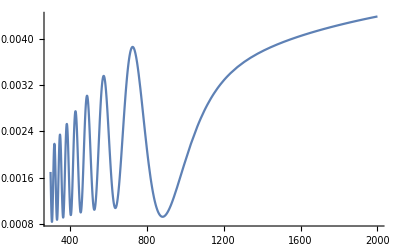

```mathematica
ph[x_,q_]:=2*NIntegrate[BesselJ[0,z*Sqrt[1-(u/bf)^2]]*Exp[I*Pi*u^2*(p+q)/(4*p*q*lambda)]*Cos[u*Pi*(x+0.5*bf*(1-q/p))/(lambda*q)],
 {u,0,bf}];

Plot[Abs[ph[-bf*0.5*(1-q/p),q]^2]/(lambda*(p+q)),{q,0.3*10^3,2*10^3},PlotRange->All,AxesOrigin->{1*10^3,0}]
```